```mathematica
FullSimplify[Integrate[Integrate[Integrate[Integrate[r1 r2 Sqrt[r1^2+r2^2-2 r1 r2 Cos[alpha-beta]],{r1,0,1}],{r2,0,1}],{alpha,0,2Pi}],{beta,0,2Pi}]]
```

$Aborted

```mathematica
FullSimplify[Integrate[r1 r2 Sqrt[r1^2+r2^2-2 r1 r2 Cos[alpha-beta]],r1]]
```

1/12 r2 (√(r1^2+r2^2-2 r1 r2 Cos[alpha-beta]) (4 r1^2+r2^2-2 r1 r2 Cos[alpha-beta]-3 r2^2 Cos[2 (alpha-beta)])+6 r2^3 Cos[alpha-beta] Log[r1-r2 Cos[alpha-beta]+√(r1^2+r2^2-2 r1 r2 Cos[alpha-beta])] Sin[alpha-beta]^2)

```mathematica
FullSimplify[1/12 r2 (√(r1^2+r2^2-2 r1 r2 Cos[alpha-beta]) (4 r1^2+r2^2-2 r1 r2 Cos[alpha-beta]-3 r2^2 Cos[2 (alpha-beta)])+6 r2^3 Cos[alpha-beta] Log[r1-r2 Cos[alpha-beta]+√(r1^2+r2^2-2 r1 r2 Cos[alpha-beta])] Sin[alpha-beta]^2) /. r1->1]
```

1/12 r2 (√(1+r2^2-2 r2 Cos[alpha-beta]) (4+r2^2-2 r2 Cos[alpha-beta]-3 r2^2 Cos[2 (alpha-beta)])+6 r2^3 Cos[alpha-beta] Log[1-r2 Cos[alpha-beta]+√(1+r2^2-2 r2 Cos[alpha-beta])] Sin[alpha-beta]^2)

```mathematica
FullSimplify[1/12 r2 (√(r1^2+r2^2-2 r1 r2 Cos[alpha-beta]) (4 r1^2+r2^2-2 r1 r2 Cos[alpha-beta]-3 r2^2 Cos[2 (alpha-beta)])+6 r2^3 Cos[alpha-beta] Log[r1-r2 Cos[alpha-beta]+√(r1^2+r2^2-2 r1 r2 Cos[alpha-beta])] Sin[alpha-beta]^2) /. r1->0]
```

1/12 r2 ((r2^2)^(3/2)-3 (r2^2)^(3/2) Cos[2 (alpha-beta)]+6 r2^3 Cos[alpha-beta] Log[√(r2^2)-r2 Cos[alpha-beta]] Sin[alpha-beta]^2)

```mathematica
FullSimplify[1/12 r2 (√(1+r2^2-2 r2 Cos[alpha-beta]) (4+r2^2-2 r2 Cos[alpha-beta]-3 r2^2 Cos[2 (alpha-beta)])+6 r2^3 Cos[alpha-beta] Log[1-r2 Cos[alpha-beta]+√(1+r2^2-2 r2 Cos[alpha-beta])] Sin[alpha-beta]^2)-(1/12 r2 (r2^3-3 r2^3 Cos[2 (alpha-beta)]+6 r2^3 Cos[alpha-beta] Log[r2-r2 Cos[alpha-beta]] Sin[alpha-beta]^2))]
```

1/12 r2 (-r2^3+3 r2^3 Cos[2 (alpha-beta)]+√(1+r2^2-2 r2 Cos[alpha-beta]) (4+r2^2-2 r2 Cos[alpha-beta]-3 r2^2 Cos[2 (alpha-beta)])-6 r2^3 Cos[alpha-beta] Log[r2-r2 Cos[alpha-beta]] Sin[alpha-beta]^2+6 r2^3 Cos[alpha-beta] Log[1-r2 Cos[alpha-beta]+√(1+r2^2-2 r2 Cos[alpha-beta])] Sin[alpha-beta]^2)

```mathematica
FullSimplify[Integrate[1/12 r2 (-r2^3+3 r2^3 Cos[2 (alpha-beta)]+√(1+r2^2-2 r2 Cos[alpha-beta]) (4+r2^2-2 r2 Cos[alpha-beta]-3 r2^2 Cos[2 (alpha-beta)])-6 r2^3 Cos[alpha-beta] Log[r2-r2 Cos[alpha-beta]] Sin[alpha-beta]^2+6 r2^3 Cos[alpha-beta] Log[1-r2 Cos[alpha-beta]+√(1+r2^2-2 r2 Cos[alpha-beta])] Sin[alpha-beta]^2),r2]]
```

1/60 (r2^5 (-1+3 Cos[2 (alpha-beta)])+√(1+r2^2-2 r2 Cos[alpha-beta]) (1+8 r2^2+r2^4-2 (r2+r2^3) Cos[alpha-beta]-3 (1+r2^4) Cos[2 (alpha-beta)])-6 r2^5 Cos[alpha-beta] Log[r2-r2 Cos[alpha-beta]] Sin[alpha-beta]^2+6 Cos[alpha-beta] Log[r2-Cos[alpha-beta]+√(1+r2^2-2 r2 Cos[alpha-beta])] Sin[alpha-beta]^2+6 r2^5 Cos[alpha-beta] Log[1-r2 Cos[alpha-beta]+√(1+r2^2-2 r2 Cos[alpha-beta])] Sin[alpha-beta]^2)

```mathematica
FullSimplify[1/60 (r2^5 (-1+3 Cos[2 (alpha-beta)])+√(1+r2^2-2 r2 Cos[alpha-beta]) (1+8 r2^2+r2^4-2 (r2+r2^3) Cos[alpha-beta]-3 (1+r2^4) Cos[2 (alpha-beta)])-6 r2^5 Cos[alpha-beta] Log[r2-r2 Cos[alpha-beta]] Sin[alpha-beta]^2+6 Cos[alpha-beta] Log[r2-Cos[alpha-beta]+√(1+r2^2-2 r2 Cos[alpha-beta])] Sin[alpha-beta]^2+6 r2^5 Cos[alpha-beta] Log[1-r2 Cos[alpha-beta]+√(1+r2^2-2 r2 Cos[alpha-beta])] Sin[alpha-beta]^2)/. r2->1]
```

1/60 (-1+√(2-2 Cos[alpha-beta]) (10-4 Cos[alpha-beta]-6 Cos[2 (alpha-beta)])+3 Cos[2 (alpha-beta)]-6 Cos[alpha-beta] Log[1-Cos[alpha-beta]] Sin[alpha-beta]^2+12 Cos[alpha-beta] Log[1+√(2-2 Cos[alpha-beta])-Cos[alpha-beta]] Sin[alpha-beta]^2)

```mathematica
FullSimplify[1/60 (r2^5 (-1+3 Cos[2 (alpha-beta)])+√(1+r2^2-2 r2 Cos[alpha-beta]) (1+8 r2^2+r2^4-2 (r2+r2^3) Cos[alpha-beta]-3 (1+r2^4) Cos[2 (alpha-beta)])+6 Cos[alpha-beta] Log[r2-Cos[alpha-beta]+√(1+r2^2-2 r2 Cos[alpha-beta])] Sin[alpha-beta]^2+6 r2^5 Cos[alpha-beta] Log[1-r2 Cos[alpha-beta]+√(1+r2^2-2 r2 Cos[alpha-beta])] Sin[alpha-beta]^2) /. r2->0]
```

1/60 (1-3 Cos[2 (alpha-beta)]+6 Cos[alpha-beta] Log[1-Cos[alpha-beta]] Sin[alpha-beta]^2)

```mathematica
FullSimplify[1/60 (-1+√(2-2 Cos[alpha-beta]) (10-4 Cos[alpha-beta]-6 Cos[2 (alpha-beta)])+3 Cos[2 (alpha-beta)]-6 Cos[alpha-beta] Log[1-Cos[alpha-beta]] Sin[alpha-beta]^2+12 Cos[alpha-beta] Log[1+√(2-2 Cos[alpha-beta])-Cos[alpha-beta]] Sin[alpha-beta]^2)-(1/60 (1-3 Cos[2 (alpha-beta)]+6 Cos[alpha-beta] Log[1-Cos[alpha-beta]] Sin[alpha-beta]^2))]
```

1/30 (-1+5 √(2-2 Cos[alpha-beta])-3 (-1+√(2-2 Cos[alpha-beta])) Cos[2 (alpha-beta)]-2 Cos[alpha-beta] (√(2-2 Cos[alpha-beta])+3 (Log[1-Cos[alpha-beta]]-Log[1+√(2-2 Cos[alpha-beta])-Cos[alpha-beta]]) Sin[alpha-beta]^2))

```mathematica
FullSimplify[Integrate[-1-10 Sin[alpha/2]-3 (-1-2 Sin[alpha/2]) Cos[2 alpha]-2 Cos[alpha] (-2 Sin[alpha/2]+3 (Log[1-Cos[alpha]]-Log[1-2 Sin[alpha/2]-Cos[alpha]]) Sin[alpha]^2),alpha]]
```

22 Cos[alpha/2]+1/3 Cos[(3 alpha)/2]-Cos[(5 alpha)/2]+2 (-Log[1-Cos[alpha]]+Log[1-Cos[alpha]-2 Sin[alpha/2]]) Sin[alpha]^3+Sin[2 alpha]

```mathematica
FullSimplify[22 Cos[alpha/2]+1/3 Cos[(3 alpha)/2]-Cos[(5 alpha)/2]+Sin[2 alpha]/. alpha->0]
```

64/3

```mathematica
FullSimplify[22 Cos[alpha/2]+1/3 Cos[(3 alpha)/2]-Cos[(5 alpha)/2]+2 (-Log[1-Cos[alpha]]+Log[1-Cos[alpha]-2 Sin[alpha/2]]) Sin[alpha]^3+Sin[2 alpha]/. alpha->-beta]
```

1/3 (66 Cos[beta/2]+Cos[(3 beta)/2]-3 (Cos[(5 beta)/2]+2 (-Log[1-Cos[beta]]+Log[1-Cos[beta]+2 Sin[beta/2]]) Sin[beta]^3+Sin[2 beta]))

```mathematica
Integrate[64/3-(1/3 (66 Cos[beta/2]+Cos[(3 beta)/2]-3 (Cos[(5 beta)/2]+2 (-Log[1-Cos[beta]]+Log[1-Cos[beta]+2 Sin[beta/2]]) Sin[beta]^3+Sin[2 beta]))),{beta,0,2Pi}]
```

(128 π)/3

```mathematica
FullSimplify[Integrate[-1+10 Sin[alpha/2]-3 (-1+2 Sin[alpha/2]) Cos[2 alpha]-2 Cos[alpha] (2 Sin[alpha/2]+3 (Log[1-Cos[alpha]]-Log[1+2 Sin[alpha/2]-Cos[alpha]]) Sin[alpha]^2),alpha]]
```

-22 Cos[alpha/2]-1/3 Cos[(3 alpha)/2]+Cos[(5 alpha)/2]+2 (-Log[1-Cos[alpha]]+Log[1-Cos[alpha]+2 Sin[alpha/2]]) Sin[alpha]^3+Sin[2 alpha]

```mathematica
FullSimplify[-22 Cos[alpha/2]-1/3 Cos[(3 alpha)/2]+Cos[(5 alpha)/2]+Sin[2 alpha] /. alpha->0]
```

-64/3

```mathematica
FullSimplify[-22 Cos[alpha/2]-1/3 Cos[(3 alpha)/2]+Cos[(5 alpha)/2]+2 (-Log[1-Cos[alpha]]+Log[1-Cos[alpha]+2 Sin[alpha/2]]) Sin[alpha]^3+Sin[2 alpha] /. alpha->2Pi-beta]
```

22 Cos[beta/2]+1/3 Cos[(3 beta)/2]-Cos[(5 beta)/2]-2 Cos[beta] Sin[beta]+2 (Log[1-Cos[beta]]-Log[1-Cos[beta]+2 Sin[beta/2]]) Sin[beta]^3

```mathematica
Integrate[22 Cos[beta/2]+1/3 Cos[(3 beta)/2]-Cos[(5 beta)/2]-2 Cos[beta] Sin[beta]+2 (Log[1-Cos[beta]]-Log[1-Cos[beta]+2 Sin[beta/2]]) Sin[beta]^3+64/3,{beta,0,2Pi}]
```

(128 π)/3

```mathematica
N[128 Pi 2/(3 30 Pi^2)]
```

```mathematica
FullSimplify[128 Pi 2/(3 30 Pi^2)]
```

128/(45 π)

```mathematica
N[%]
```

0.905415

## Quadrat

```mathematica
Integrate[Integrate[Integrate[Integrate[Sqrt[(x1-x2)^2+(y1-y2)^2],{y2,0,1}],{y1,0,1}],{x2,0,1}],{x1,0,1}]
```

$Aborted

```mathematica
FullSimplify[Integrate[Sqrt[(x1-x2)^2+(y1-y2)^2],y2]]
```

1/2 (√((x1-x2)^2+(y1-y2)^2) (-y1+y2)-(x1-x2)^2 Log[y1+√((x1-x2)^2+(y1-y2)^2)-y2])

```mathematica
FullSimplify[1/2 (√((x1-x2)^2+(y1-y2)^2) (-y1+y2)-(x1-x2)^2 Log[y1+√((x1-x2)^2+(y1-y2)^2)-y2]) /. y2->1]
```

1/2 (-√((x1-x2)^2+(-1+y1)^2) (-1+y1)-(x1-x2)^2 Log[-1+√((x1-x2)^2+(-1+y1)^2)+y1])

```mathematica
FullSimplify[1/2 (√((x1-x2)^2+(y1-y2)^2) (-y1+y2)-(x1-x2)^2 Log[y1+√((x1-x2)^2+(y1-y2)^2)-y2]) /. y2->0]
```

1/2 (-y1 √((x1-x2)^2+y1^2)-(x1-x2)^2 Log[y1+√((x1-x2)^2+y1^2)])

```mathematica
FullSimplify[1/2 (-√((x1-x2)^2+(-1+y1)^2) (-1+y1)-(x1-x2)^2 Log[-1+√((x1-x2)^2+(-1+y1)^2)+y1])-(1/2 (-y1 √((x1-x2)^2+y1^2)-(x1-x2)^2 Log[y1+√((x1-x2)^2+y1^2)]))]
```

1/2 (-√((x1-x2)^2+(-1+y1)^2) (-1+y1)-(x1-x2)^2 Log[-1+√((x1-x2)^2+(-1+y1)^2)+y1])+1/2 (y1 √((x1-x2)^2+y1^2)+(x1-x2)^2 Log[y1+√((x1-x2)^2+y1^2)])

```mathematica
FullSimplify[Integrate[1/2 (-√((x1-x2)^2+(-1+y1)^2) (-1+y1)-(x1-x2)^2 Log[-1+√((x1-x2)^2+(-1+y1)^2)+y1])+1/2 (y1 √((x1-x2)^2+y1^2)+(x1-x2)^2 Log[y1+√((x1-x2)^2+y1^2)]),y1]]
```

1/2 (1/3 (2 (x1-x2)^2-(-1+y1)^2) √((x1-x2)^2+(-1+y1)^2)+1/3 (-2 (x1-x2)^2+y1^2) √((x1-x2)^2+y1^2)-(x1-x2)^2 (-1+y1) Log[-1+√((x1-x2)^2+(-1+y1)^2)+y1]+(x1-x2)^2 y1 Log[y1+√((x1-x2)^2+y1^2)])

```mathematica
FullSimplify[1/2 (1/3 (2 (x1-x2)^2-(-1+y1)^2) √((x1-x2)^2+(-1+y1)^2)+1/3 (-2 (x1-x2)^2+y1^2) √((x1-x2)^2+y1^2)-(x1-x2)^2 (-1+y1) Log[-1+√((x1-x2)^2+(-1+y1)^2)+y1]+(x1-x2)^2 y1 Log[y1+√((x1-x2)^2+y1^2)])/. y1->1]
```

1/6 ((1-2 (x1-x2)^2) √(1+(x1-x2)^2)+2 ((x1-x2)^2)^(3/2)+3 (x1-x2)^2 Log[1+√(1+(x1-x2)^2)])

```mathematica
FullSimplify[1/2 (1/3 (2 (x1-x2)^2-(-1+y1)^2) √((x1-x2)^2+(-1+y1)^2)+1/3 (-2 (x1-x2)^2+y1^2) √((x1-x2)^2+y1^2)-(x1-x2)^2 (-1+y1) Log[-1+√((x1-x2)^2+(-1+y1)^2)+y1]+(x1-x2)^2 y1 Log[y1+√((x1-x2)^2+y1^2)])/. y1->0]
```

1/6 (√(1+(x1-x2)^2) (-1+2 (x1-x2)^2)-2 ((x1-x2)^2)^(3/2)+3 (x1-x2)^2 Log[-1+√(1+(x1-x2)^2)])

```mathematica
FullSimplify[1/6 ((1-2 (x1-x2)^2) √(1+(x1-x2)^2)+2 ((x1-x2)^2)^(3/2)+3 (x1-x2)^2 Log[1+√(1+(x1-x2)^2)])-(1/6 (√(1+(x1-x2)^2) (-1+2 (x1-x2)^2)-2 ((x1-x2)^2)^(3/2)+3 (x1-x2)^2 Log[-1+√(1+(x1-x2)^2)]))]
```

1/6 (2 (1-2 (x1-x2)^2) √(1+(x1-x2)^2)+4 ((x1-x2)^2)^(3/2)-3 (x1-x2)^2 Log[-1+√(1+(x1-x2)^2)]+3 (x1-x2)^2 Log[1+√(1+(x1-x2)^2)])

```mathematica
FullSimplify[Integrate[1/6 (2 (1-2 (x1-x2)^2) √(1+(x1-x2)^2)+4 ((x1-x2)^2)^(3/2)-3 (x1-x2)^2 Log[-1+√(1+(x1-x2)^2)]+3 (x1-x2)^2 Log[1+√(1+(x1-x2)^2)]),x2]]
```

1/12 (-ArcSinh[x1-x2]+(x1-x2) (-3 √(1+(x1-x2)^2)+2 (√(1+(x1-x2)^2)-√((x1-x2)^2)) (x1-x2)^2+2 (x1-x2)^2 (Log[-1+√(1+(x1-x2)^2)]-Log[1+√(1+(x1-x2)^2)])))

```mathematica
FullSimplify[1/12 (-ArcSinh[x1-x2]+(x1-x2) (-3 √(1+(x1-x2)^2)+2 (√(1+(x1-x2)^2)-√((x1-x2)^2)) (x1-x2)^2+2 (x1-x2)^2 (Log[-1+√(1+(x1-x2)^2)]-Log[1+√(1+(x1-x2)^2)])))/. x2->1]
```

1/12 (ArcSinh[1-x1]+(-1+x1) (-3 √(1+(-1+x1)^2)+2 (√(1+(-1+x1)^2)-√((-1+x1)^2)) (-1+x1)^2+2 (-1+x1)^2 (Log[-1+√(1+(-1+x1)^2)]-Log[1+√(1+(-1+x1)^2)])))

```mathematica
FullSimplify[1/12 (-ArcSinh[x1-x2]+(x1-x2) (-3 √(1+(x1-x2)^2)+2 (√(1+(x1-x2)^2)-√((x1-x2)^2)) (x1-x2)^2+2 (x1-x2)^2 (Log[-1+√(1+(x1-x2)^2)]-Log[1+√(1+(x1-x2)^2)])))/. x2->0]
```

1/12 (-ArcSinh[x1]+x1 (-2 (x1^2)^(3/2)-3 √(1+x1^2)+2 x1^2 √(1+x1^2)+2 x1^2 (Log[-1+√(1+x1^2)]-Log[1+√(1+x1^2)])))

```mathematica
FullSimplify[1/12 (ArcSinh[1-x1]+(-1+x1) (-3 √(1+(-1+x1)^2)+2 (√(1+(-1+x1)^2)-√((-1+x1)^2)) (-1+x1)^2+2 (-1+x1)^2 (Log[-1+√(1+(-1+x1)^2)]-Log[1+√(1+(-1+x1)^2)])))-(1/12 (-ArcSinh[x1]+x1 (-2 x1^3-3 √(1+x1^2)+2 x1^2 √(1+x1^2)+2 x1^2 (Log[-1+√(1+x1^2)]-Log[1+√(1+x1^2)]))))]
```

1/12 (2 x1^4+3 x1 √(1+x1^2)-2 x1^3 √(1+x1^2)+ArcSinh[1-x1]+ArcSinh[x1]+(-1+x1) (-3 √(2+(-2+x1) x1)+2 (-1+x1)^2 (-√((-1+x1)^2)+√(2+(-2+x1) x1))+2 (-1+x1)^2 (Log[-1+√(1+(-1+x1)^2)]-Log[1+√(1+(-1+x1)^2)]))-2 x1^3 Log[-1+√(1+x1^2)]+2 x1^3 Log[1+√(1+x1^2)])

```mathematica
FullSimplify[Integrate[1/12 (2 x1^4+3 x1 √(1+x1^2)-2 x1^3 √(1+x1^2)+ArcSinh[1-x1]+ArcSinh[x1]+(-1+x1) (-3 √(2+(-2+x1) x1)+2 (-1+x1)^2 (-√((-1+x1)^2)+√(2+(-2+x1) x1))+2 (-1+x1)^2 (Log[-1+√(1+(-1+x1)^2)]-Log[1+√(1+(-1+x1)^2)]))-2 x1^3 Log[-1+√(1+x1^2)]+2 x1^3 Log[1+√(1+x1^2)]),x1]]
```

1/120 (-4 (-1+x1)^4 √((-1+x1)^2)+4 x1^5+20 √(2+(-2+x1) x1)-20 (2+(-2+x1) x1)^(3/2)+4 (2+(-2+x1) x1)^(5/2)-20 √(1+x1^2)+20 (1+x1^2)^(3/2)-4 (1+x1^2)^(5/2)-10 ArcSinh[1-x1]+10 x1 ArcSinh[1-x1]+10 x1 ArcSinh[x1]-10 ArcTanh[√(2+(-2+x1) x1)]+10 ArcTanh[√(1+x1^2)]+5 (-2+x1) x1 (2+(-2+x1) x1) Log[-1+√(1+(-1+x1)^2)]-5 (-2+x1) x1 (2+(-2+x1) x1) Log[1+√(1+(-1+x1)^2)]-5 (-1+x1^4) Log[-1+√(1+x1^2)]+5 (-1+x1^4) Log[1+√(1+x1^2)])

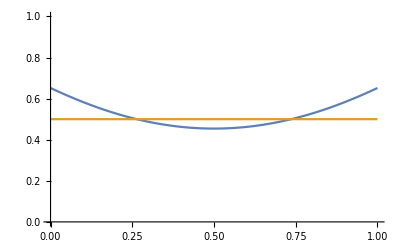

```mathematica
Plot[{1/12 (2 x1^4+3 x1 √(1+x1^2)-2 x1^3 √(1+x1^2)+ArcSinh[1-x1]+ArcSinh[x1]+(-1+x1) (-3 √(2+(-2+x1) x1)+2 (-1+x1)^2 (-√((-1+x1)^2)+√(2+(-2+x1) x1))+2 (-1+x1)^2 (Log[-1+√(1+(-1+x1)^2)]-Log[1+√(1+(-1+x1)^2)]))-2 x1^3 Log[-1+√(1+x1^2)]+2 x1^3 Log[1+√(1+x1^2)]),1/2},{x1,0,1},PlotRange->{0,1}]
```

```mathematica
FullSimplify[1/120 (-4 (-1+x1)^4 √((-1+x1)^2)+4 x1^5+20 √(2+(-2+x1) x1)-20 (2+(-2+x1) x1)^(3/2)+4 (2+(-2+x1) x1)^(5/2)-20 √(1+x1^2)+20 (1+x1^2)^(3/2)-4 (1+x1^2)^(5/2)-10 ArcSinh[1-x1]+10 x1 ArcSinh[1-x1]+10 x1 ArcSinh[x1]-10 ArcTanh[√(2+(-2+x1) x1)]+10 ArcTanh[√(1+x1^2)]+5 (-2+x1) x1 (2+(-2+x1) x1) Log[-1+√(1+(-1+x1)^2)]-5 (-2+x1) x1 (2+(-2+x1) x1) Log[1+√(1+(-1+x1)^2)]-5 (-1+x1^4) Log[-1+√(1+x1^2)]+5 (-1+x1^4) Log[1+√(1+x1^2)]) /. x1->1]
```

Infinity::indet: Indeterminate expression 8 - 20\ √2 - 16\ √2 + 40\ √2 + 10\ ArcSinh[1] + 10\ ArcTanh[√2] + -∞ + ∞ + 5\ Log[2] encountered.

Indeterminate

```mathematica
Limit[1/120 (-4 (-1+x1)^4 √((-1+x1)^2)+4 x1^5+20 √(2+(-2+x1) x1)-20 (2+(-2+x1) x1)^(3/2)+4 (2+(-2+x1) x1)^(5/2)-20 √(1+x1^2)+20 (1+x1^2)^(3/2)-4 (1+x1^2)^(5/2)-10 ArcSinh[1-x1]+10 x1 ArcSinh[1-x1]+10 x1 ArcSinh[x1]-10 ArcTanh[√(2+(-2+x1) x1)]+10 ArcTanh[√(1+x1^2)]+5 (-2+x1) x1 (2+(-2+x1) x1) Log[-1+√(1+(-1+x1)^2)]-5 (-2+x1) x1 (2+(-2+x1) x1) Log[1+√(1+(-1+x1)^2)]-5 (-1+x1^4) Log[-1+√(1+x1^2)]+5 (-1+x1^4) Log[1+√(1+x1^2)]),x1->1]
```

1/120 (8+4 √2+5 ⅈ π+10 ArcSinh[1]+10 ArcTanh[√2])

```mathematica
Limit[1/120 (-4 (-1+x1)^4 √((-1+x1)^2)+4 x1^5+20 √(2+(-2+x1) x1)-20 (2+(-2+x1) x1)^(3/2)+4 (2+(-2+x1) x1)^(5/2)-20 √(1+x1^2)+20 (1+x1^2)^(3/2)-4 (1+x1^2)^(5/2)-10 ArcSinh[1-x1]+10 x1 ArcSinh[1-x1]+10 x1 ArcSinh[x1]-10 ArcTanh[√(2+(-2+x1) x1)]+10 ArcTanh[√(1+x1^2)]+5 (-2+x1) x1 (2+(-2+x1) x1) Log[-1+√(1+(-1+x1)^2)]-5 (-2+x1) x1 (2+(-2+x1) x1) Log[1+√(1+(-1+x1)^2)]-5 (-1+x1^4) Log[-1+√(1+x1^2)]+5 (-1+x1^4) Log[1+√(1+x1^2)]),x1->0]
```

1/120 (-5 ⅈ π-2 (4+2 √2+5 ArcSinh[1]+5 ArcTanh[√2]))

```mathematica
FullSimplify[1/120 (8+4 √2+5 ⅈ π+10 ArcSinh[1]+10 ArcTanh[√2])-(1/120 (-5 ⅈ π-2 (4+2 √2+5 ArcSinh[1]+5 ArcTanh[√2])))]
```

1/30 (4+2 √2+5 ArcSinh[2 √2])

```mathematica
N[%]
```

0.521405